```mathematica
Sentiment Analysis of Amazon Reviews
```

Amazon Analysis of Reviews Sentiment

## Getting input data:

```mathematica
raw=OpenRead["D:\\studies\\USC\\Syllabus\\Summer 2017\\AI\\hw3\\reviews.csv"]
data=Map[StringSplit[#,"|"]&,ReadList[raw,String]]
test=Take[data,{1,-1,5}]
train=Drop[data,{1,-1,5}]
```

InputStream[…]

{{label,text},399999,{negative,Comedy Scene, and Not Heard: This DVD will be a disappointment if you get it hoping to see some substantial portion of the acts of the various comics listed on the cover. All you get here are snippets of performance, at best. The rest is just loose-leaf reminiscence about the good old days in B…etrated - back then. But you had to have been there to appreciate all the basically good ol' boy camaraderie. If you weren't actually a part of that scene, all this joshing and jostling will fall flat.If you want to actually hear some of these comics' routines - you will have to look elsewhere.}}
 |  |  |  |

{{label,text},79999,{negative,Comedy Scene, and Not Heard: This DVD will be a disappointment if you get it hoping to see some substantial portion of the acts of the various comics listed on the cover. All you get here are snippets of performance, at best. The rest is just loose-leaf reminiscence about the good old days in B…etrated - back then. But you had to have been there to appreciate all the basically good ol' boy camaraderie. If you weren't actually a part of that scene, all this joshing and jostling will fall flat.If you want to actually hear some of these comics' routines - you will have to look elsewhere.}}
 |  |  |  |

{{positive,Great CD: My lovely Pat has one of the GREAT voices of her generation. I have listened to this CD for YEARS and I still LOVE IT. When I'm in a good mood it makes me feel better. A bad mood just evaporates like sugar in the rain. This CD just oozes LIFE. Vocals are jusat STUUNNING and lyrics just kill. One of life's hidden gems. This is a desert isle CD in my book. Why she never made it big is just beyond me. Everytime I play this, no matter black, white, young, old, male, female EVERYBODY says one thing "Who was that singing ?"},319998,{positive,Classic Jessica Mitford: Thi… a complete delight to read.}}
 |  |  |  |

Partitioning the data:
Here we drop the first label/reviews in the first line.

```mathematica
test=Drop[test,1]
```

{{positive,Great for the non-audiophile: Reviewed quite a bit of the combo players and was hesitant due to unfavorable reviews and size of machines. I am weaning off my VHS collection, but don't want to replace them with DVD's. This unit is well built, easy to setup and resolution and special effects (no progressive scan for HDTV owners) suitable for many people looking for a versatile product.Cons- No universal remote.},79998,{negative,Comedy Scene, and Not Heard: This DVD will be a disappointment if you get it hoping to se…ou want to actually hear some of these comics' routines - you will have to look elsewhere.}}
 |  |  |  |

## Dataset size : 2000

```mathematica
test=Take[test,400];
train=Take[train,1600]
```

{{positive,Great CD: My lovely Pat has one of the GREAT voices of her generation. I have listened to this CD for YEARS and I still LOVE IT. When I'm in a good mood it makes me feel better. A bad mood just evaporates like sugar in the rain. This CD just oozes LIFE. Vocals are jusat STUUNNING and lyrics just kill. One of life's hidden gems. This is a desert isle CD in my book. Why she never made it big is just beyond me. Everytime I play this, no matter black, white, young, old, male, female EVERYBODY says one thing "Who was that singing ?"},1598,{positive,Great Children's Story: The P… over and over again as well.}}
 |  |  |  |

Split the labels and reviews into label list and commentList

```mathematica
labelList=train[[All,1]];
commentList=train[[All,2]];
```

## PreProcessing and Feature Extraction:

Get all the default StopWords

```mathematica
stopWords=WordData[All,"Stopwords"];
```

Delete Unwanted StopWords from the list obtained above and add highest frequency words which does not affect classification found to the StopWords list.

```mathematica
deleteFromStopWords={"aren't","before","but","can","cannot","can't","could","couldn't","did","didn't","do","does","doesn't","don't","had","hadn't","has","hasn't","have","haven't","having","if","isn't","no","not","perhaps","since","though","was","wasn't","were","weren't","won't","would","wouldn't"};

newStopWords=Complement[stopWords,deleteFromStopWords];

customStopWords={"this","product","item","url","link","book","movie","read","album","review","world","things","christmas","children","reading","books","movies","story","money","film","year","life","pages","dvd","cd","sony","night","thing","music","series","price","edition","author","novel"};

newStopWords=Union[newStopWords,customStopWords]
```

{0,1,2,3,4,5,6,7,8,9,a,A,about,above,across,after,again,against,album,all,almost,alone,along,already,also,although,always,am,among,an,and,another,any,anyone,anything,anywhere,are,around,as,at,author,b,B,back,be,became,because,become,becomes,been,behind,being,below,between,book,books,both,by,c,C,cd,children,christmas,d,D,doing,done,down,during,dvd,e,E,each,edition,either,enough,even,ever,every,everyone,everything,everywhere,f,F,few,film,find,first,for,four,from,full,further,g,G,get,give,go,h,H,he,he'd,he'll,her,here,here's,hers,herself,he's,him,himself,his,how,however,how's,i,I,i'd,i'll,i'm,in,interest,into,is,it,item,it's,its,itself,i've,j,J,k,K,keep,l,L,last,least,less,let's,life,link,m,M,made,many,may,me,might,money,more,most,mostly,movie,movies,much,music,must,mustn't,my,myself,n,N,never,next,night,nobody,noone,nor,nothing,novel,now,nowhere,o,O,of,off,often,on,once,one,only,or,other,others,ought,our,ours,ourselves,out,over,own,p,P,pages,part,per,price,product,put,q,Q,r,R,rather,read,reading,review,s,S,same,see,seem,seemed,seeming,seems,series,several,shan't,she,she'd,she'll,she's,should,shouldn't,show,side,so,some,someone,something,somewhere,sony,still,story,such,t,T,take,than,that,that's,the,their,theirs,them,themselves,then,there,therefore,there's,these,they,they'd,they'll,they're,they've,thing,things,this,those,three,through,thus,to,together,too,toward,two,u,U,under,until,up,upon,url,us,v,V,very,w,W,we,we'd,we'll,well,we're,we've,what,what's,when,when's,where,where's,whether,which,while,who,whole,whom,who's,whose,why,why's,will,with,within,without,world,x,X,y,Y,year,yet,you,you'd,you'll,your,you're,yours,yourself,yourselves,you've,z,Z}

Necessary function and variables : getFilteredSentence function removes the StopWords and numbers in the given string

```mathematica
vowel=Characters@"aeiou"

getFilteredSentence[str_]:=
Select[str,Not[MemberQ[newStopWords,#]]&& Not[DigitQ[#]]&];
```

{a,e,i,o,u}

Lowercase and Remove Diacritics

```mathematica
AbsoluteTiming[commentList=ParallelMap[ToLowerCase[RemoveDiacritics[#]]&,commentList]];
```

Replace  Emoticons with appropriate words , Remove symbols and Replace low frequency negative words with “not” a high frequency negative word.

```mathematica
AbsoluteTiming[commentList=ParallelMap[StringReplace[#,{":)"|";)"|"0:-)"|":D"|":*"|":o"|":P"->"happy",":("|">:("|";("|">:)
"|" D:<"|":|
"|">:/"->"sad","can’t"|"don’t"|"isn’t"|"never"|"cannot"->"not","["|"]"|"{"|"}"|"("|")"|"-"|"_"|"<"|">"|"$"|"/"|"%"|"."|","|"*"->""}]&,commentList]];
```

Remove repeated vowels in the string

```mathematica
AbsoluteTiming[commentList=ParallelMap[StringReplace[#,b:vowel~Repeated~{3}~~vowel..:>b]&,commentList]];
```

Bag of words

```mathematica
AbsoluteTiming[commentList=ParallelMap[Union[TextWords[#]]&,commentList]]
```

{3.15406,{{a,and,are,bad,better,beyond,big,black,book,cd,desert,evaporates,everybody,everytime,feel,female,for,gems,generation,good,great,has,have,her,hidden,i,i'm,in,is,isle,it,jusat,just,kill,life,life's,like,listened,love,lovely,lyrics,made,makes,male,matter,me,mood,my,no,not,of,old,one,oozes,pat,play,rain,says,she,singing,still,stuunning,sugar,that,the,thing,this,to,vocals,voices,was,when,white,who,why,years,young},1598,{again,and,25,well,with}}}
 |  |  |  |

Filter the dataset

```mathematica
AbsoluteTiming[commentList=ParallelMap[getFilteredSentence,commentList]]
```

{1.02618,{{bad,better,beyond,big,black,desert,evaporates,everybody,everytime,feel,female,gems,generation,good,great,has,have,hidden,isle,jusat,just,kill,life's,like,listened,love,lovely,lyrics,makes,male,matter,mood,no,not,old,oozes,pat,play,rain,says,singing,stuunning,sugar,vocals,voices,was,white,years,young},1598,{children's,childrenthat,come,enjoy,great,greatwe,home,like,moments,precious,share,stories,visit,watching}}}
 |  |  |  |

Stemming

```mathematica
AbsoluteTiming[commentList=ParallelMap[WordStem,commentList]]
```

{0.535759,{{bad,better,beyond,big,black,desert,evapor,everybodi,everytim,feel,femal,gem,gener,good,great,ha,have,hidden,isl,jusat,just,kill,life',like,listen,love,love,lyric,make,male,matter,mood,no,not,old,ooz,pat,plai,rain,sai,sing,stuun,sugar,vocal,voic,wa,white,year,young},1598,{children',childrenthat,come,enjoi,great,greatw,home,like,moment,preciou,share,stori,visit,watch}}}
 |  |  |  |

Flatten the dataset

```mathematica
Flatten[commentList]
Flatten[labelList];
```

{bad,better,beyond,big,black,desert,evapor,everybodi,everytim,feel,femal,gem,gener,good,great,ha,have,hidden,isl,jusat,just,kill,life',like,listen,love,love,lyric,make,male,matter,mood,no,not,old,ooz,pat,plai,rain,sai,sing,52234,materi,mix,natur,natur,natur,need,phenomen,photo,put,vivid,wonder,work,worth,adventur,amaz,anim,corwin,fun,ha,interest,jeff,love,man,share,shine,word,write,children',childrenthat,come,enjoi,great,greatw,home,like,moment,preciou,share,stori,visit,watch}
 |  |  |  |

## Classify:

```mathematica
AbsoluteTiming[decisionTreeClassifier=Classify[commentList->labelList,Method->"RandomForest"]]
AbsoluteTiming[neuralNetworkClassifier=Classify[commentList->labelList,Method->"NeuralNetwork"]]
AbsoluteTiming[logisticRegressionClassifier=Classify[commentList->labelList,Method->"LogisticRegression"]]
```

{46.3701,ClassifierFunction[…]}

{1084.22,ClassifierFunction[…]}

{28.0286,ClassifierFunction[…]}

Same thing is repeated for test set.

```mathematica
resultCommentList=test[[All,2]];

AbsoluteTiming[resultCommentList=ParallelMap[ToLowerCase[RemoveDiacritics[#]]&,resultCommentList]];

AbsoluteTiming[resultCommentList=ParallelMap[StringReplace[#,{":)"|";)"|"0:-)"|":D"|":*"|":o"|":P"->"happy",":("|">:("|";("|">:)
"|" D:<"|":|
"|">:/"->"sad","can’t"|"don’t"|"isn’t"|"never"|"cannot"->"not","["|"]"|"{"|"}"|"("|")"|"-"|"_"|"<"|">"|"$"|"/"|"%"|"."|","|"*"->""}]&,resultCommentList]];

AbsoluteTiming[resultCommentList=ParallelMap[StringReplace[#,b:vowel~Repeated~{3}~~vowel..:>b]&,resultCommentList]];

AbsoluteTiming[resultCommentList=ParallelMap[Union[TextWords[#]]&,resultCommentList]]

AbsoluteTiming[resultCommentList=ParallelMap[getFilteredSentence,resultCommentList]]

AbsoluteTiming[resultCommentList=ParallelMap[WordStem,resultCommentList]]

Flatten[resultCommentList];

resultLabelList=test[[All,1]];

Flatten[resultLabelList];

testSet=resultCommentList->resultLabelList
```

{1.02246,{{a,am,and,bit,built,but,collection,combo,don't,due,dvd's,easy,effects,for,great,hdtv,hesitant,i,is,looking,machines,many,my,no,nonaudiophile,of,off,owners,people,players,productcons,progressive,quite,remote,replace,resolution,reviewed,reviews,scan,setup,size,special,suitable,the,them,this,to,unfavorable,unit,universal,versatile,vhs,want,was,weaning,well,with},398,{a,across,alertative,alternative,an,another,any,35,truth,unraveling,warthe,where,while,will,world}}}
 |  |  |  |

{0.3107,{{bit,built,but,collection,combo,don't,due,dvd's,easy,effects,great,hdtv,hesitant,looking,machines,no,nonaudiophile,owners,people,players,productcons,progressive,quite,remote,replace,resolution,reviewed,reviews,scan,setup,size,special,suitable,unfavorable,unit,universal,versatile,vhs,want,was,weaning},398,{alertative,alternative,biggest,clues,crisis,cuban,ended,good,history,just,known,4,pay,process,reporter,reporting,secret,spooky,stumbles,time,truth,unraveling,warthe}}}
 |  |  |  |

{0.203698,{{bit,built,but,collect,combo,don't,due,dvd',easi,effect,great,hdtv,hesit,look,machin,no,nonaudiophil,owner,peopl,player,productcon,progress,quit,remot,replac,resolut,review,review,scan,setup,size,special,suitabl,unfavor,unit,univers,versatil,vh,want,wa,wean},398,{alert,altern,biggest,clue,crisi,cuban,end,good,histori,just,known,missil,murder,newpap,oft,pai,process,report,report,secret,spooki,stumbl,time,truth,unravel,warth}}}
 |  |  |  |

{{bit,built,but,collect,combo,don't,due,dvd',easi,effect,great,hdtv,hesit,look,machin,no,nonaudiophil,owner,peopl,player,productcon,progress,quit,remot,replac,resolut,review,review,scan,setup,size,special,suitabl,unfavor,unit,univers,versatil,vh,want,wa,wean},398,{alert,altern,biggest,clue,crisi,cuban,end,good,histori,just,known,missil,murder,newpap,oft,pai,process,report,report,secret,spooki,stumbl,time,truth,unravel,warth}}→{positive,negative,396,positive,positive}
 |  |  |  |

## GetResults :

#### Decision Tree: Random Forest

0.7

<|negative→0.735294,positive→0.673913|>

<|negative→0.625,positive→0.775|>

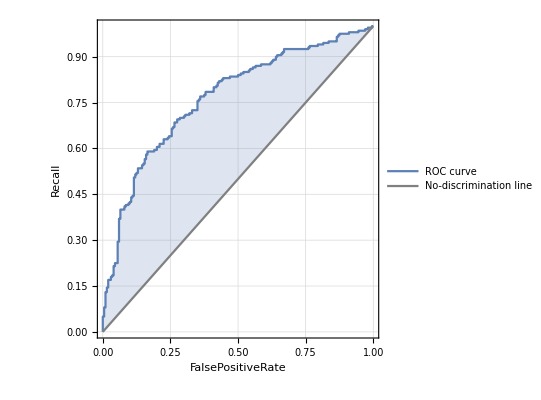
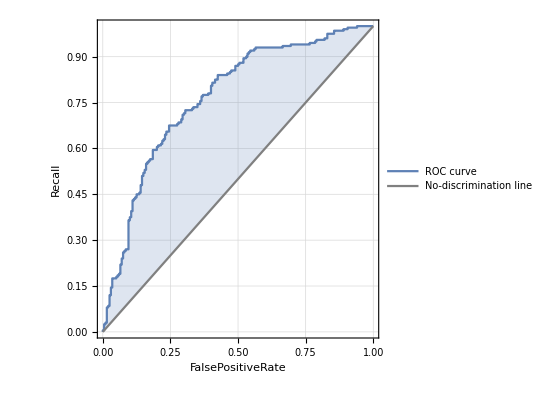
<|negative→-Graphics-,positive→-Graphics-|>

```mathematica
ClassifierMeasurements[decisionTreeClassifier,testSet,"Accuracy"]
ClassifierMeasurements[decisionTreeClassifier,testSet,"Precision"]
ClassifierMeasurements[decisionTreeClassifier,testSet,"Recall"]
ClassifierMeasurements[decisionTreeClassifier,testSet,"ROCCurve"]
```

#### Neural Networks:

0.785

<|negative→0.75,positive→0.831395|>

<|negative→0.855,positive→0.715|>

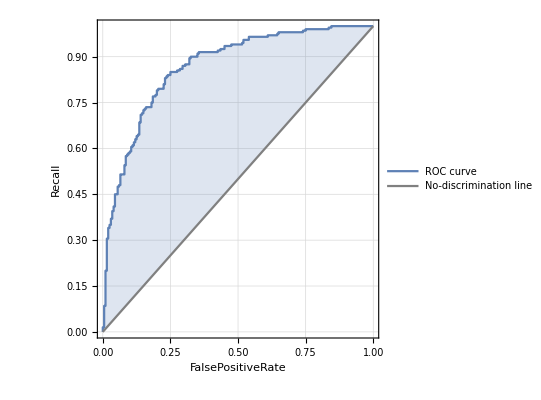
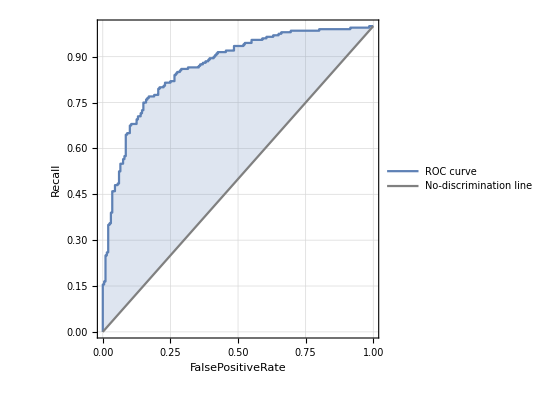
<|negative→-Graphics-,positive→-Graphics-|>

```mathematica
ClassifierMeasurements[neuralNetworkClassifier,testSet,"Accuracy"]
ClassifierMeasurements[neuralNetworkClassifier,testSet,"Precision"]
ClassifierMeasurements[neuralNetworkClassifier,testSet,"Recall"]
ClassifierMeasurements[neuralNetworkClassifier,testSet,"ROCCurve"]
```

#### Logistic Regresssion

0.805

<|negative→0.787736,positive→0.824468|>

<|negative→0.835,positive→0.775|>

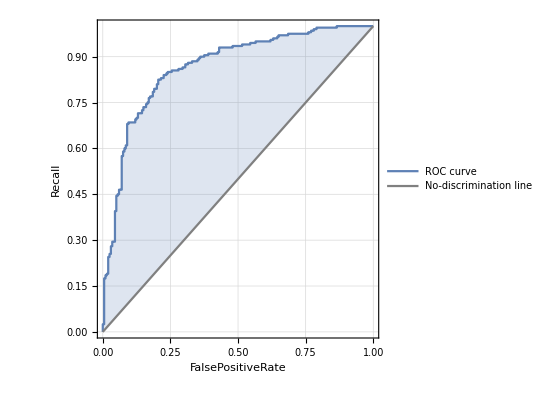
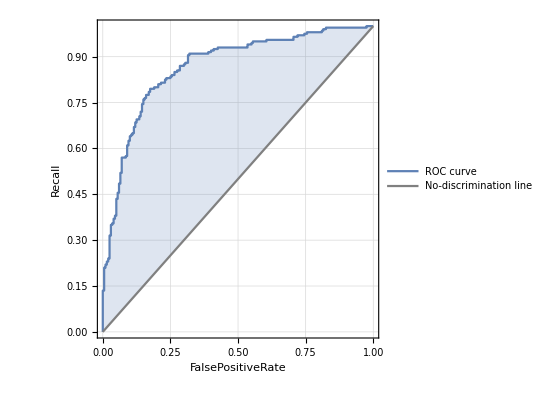
<|negative→-Graphics-,positive→-Graphics-|>

```mathematica
ClassifierMeasurements[logisticRegressionClassifier,testSet,"Accuracy"]
ClassifierMeasurements[logisticRegressionClassifier,testSet,"Precision"]
ClassifierMeasurements[logisticRegressionClassifier,testSet,"Recall"]
ClassifierMeasurements[logisticRegressionClassifier,testSet,"ROCCurve"]
```

## Description, Results and Conclusions:

#### Problem:

We have 4 lakh reviews from amazon and we need to classify them as positive and negative. This helps in determining total number of positive and negative review for an product and helps in improving the product or removing the product thus increasing the profits to the company.

#### Setting up the Data:

The data is divided into training and test set. Then it is preprocessed using several techniques.
•	Get highest frequency words in data set and remove them
•	Replace emoticons with appropriate keywords(  -> happy)
•	Remove symbols and numbers from the text.
•	Remove repeated letters in words . (coooooool->cool)
•	Bag of Words 
•	Stemming

#### Results:

Decision Tree: 
	Accuracy-> 70%
	Precision-> Positive=0.67 , Negative=0.74
	Recall-> Positive=0.78 , Negative= 0.62

Neural Network: 
	Accuracy-> 78%
	Precision-> Positive=0.83 , Negative=0.75
	Recall-> Positive=0.71 , Negative=0.85 

Logistic Regression: 
	Accuracy-> 80%
	Precision-> Positive=0.82 , Negative=0.78
	Recall-> Positive=0.77 , Negative= 0.83
Conclusions:

Logistic regression is as far the best among the three for this classification because logistic regression is for classification of things into only 2 label and here we have only 2 label i.e positive 
and negative. Also as the dataset increases the classifier becomes more accurate. This results obtained is for small dataset i.e 2000 reviews only.